# Auxiliary Functions

```mathematica
Quiet@Remove["Global`*"]
FormattingStrings[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"\\mu_{NF}"->"{muNF}"];
auxiliarystring=StringReplace[auxiliarystring,"\\omega_{NF}"->"{omegaNF}"];
auxiliarystring=ToExpression[auxiliarystring,TeXForm];
auxiliarystring=auxiliarystring/.i->I;
auxiliarystring=auxiliarystring/.OverBar[u_]->Conjugate[u];
Return[auxiliarystring]
]
FormattingStringsCommaSplit[string_]:=Block[{},
auxiliarystring=StringReplace[string,"+ "->"+"];
auxiliarystring=StringReplace[auxiliarystring," +"->"+"];
auxiliarystring=StringReplace[auxiliarystring,"- "->"-"];
auxiliarystring=StringReplace[auxiliarystring," -"->"-"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot "->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," \\cdot"->"\\cdot"];
auxiliarystring=StringReplace[auxiliarystring," "->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\cdot"->"\\times"];
auxiliarystring=StringReplace[auxiliarystring,"\\times"->" \\times "];
auxiliarystring=StringReplace[auxiliarystring,"\\mu_{NF}"->"{muNF}"];
auxiliarystring=StringReplace[auxiliarystring,"\\omega_{NF}"->"{omegaNF}"];
auxiliarystring=StringSplit[auxiliarystring,","];
Return[auxiliarystring]
]
```

# Vector field and equilibrium point

```mathematica
(*First equilibrium*)
```

```mathematica
SetDirectory[NotebookDirectory[]];
null[_String]:=Null;
eqbool=1;
If[FileExistsQ["Kinetics.txt"],
nvar=Length@ReadList["Kinetics.txt",null@String,NullRecords->True];
,
Print["The file 'Kinetics.txt' could not found. Run the Python script first."];
Quit[];
]
kinetics=Range[nvar];
var=Range[nvar];
For[varnum=1,varnum<=nvar,varnum++,
kinetics[[varnum]]=ReadLine["Kinetics.txt"];
kinetics[[varnum]]=FormattingStrings[kinetics[[varnum]]];
If[FileExistsQ["Variables.txt"],
var[[varnum]]=ReadLine["Variables.txt"];
,
Print["The file 'Variables.txt' could not be found. Run the Python script first."];
Quit[]
];
var[[varnum]]=ToExpression[var[[varnum]],TeXForm];
];
Close["Kinetics.txt"];
Close["Variables.txt"];
If[eqbool==1,
eqs=Solve[kinetics==0,var];
If[Length[eqs]>1,
aux=CreateDocument[];
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Your system has " <> ToString[Length[eqs]] <> " equilibria"}],"Output"]];
For[eqnum=1,eqnum<=Length[eqs],eqnum++,
SelectionMove[aux,Next,Cell];
NotebookWrite[aux,Cell[Row[{"Equilibrium number " <> ToString[eqnum] <> " is equal to ",ToString[eqs[[eqnum]],FormatType->StandardForm]}],"Output"]];];
eqnumber=Input["Enter the number of the equilibrium point you would like to consider. Enter 0 if the software did not find your desired homogeneous steady-state or you want to consider them all"];
NotebookClose[aux];
If[eqnumber==0,
eq={0};
,
eq=eqs[[eqnumber]]//Simplify;]
,
Print["Mathematica found only one homogeneous steady-state in your system. It will proceed with that one."];
eq=eqs[[1]]//Simplify;
]
,
eq={0};
]
```

# Fixed parameters and Turing-Wave bifurcation variables

```mathematica
If[FileExistsQ["Third-order coefficient C130.txt"],
C130=Import["Third-order coefficient C130.txt"];
,
Print["The file 'Third-order coefficient C130.txt' could not be found. Run the Python script first."];
Quit[];
]
C130=FormattingStrings[C130];
If[FileExistsQ["Third-order coefficient C112.txt"],
C112=Import["Third-order coefficient C112.txt"];
,
Print["The file 'Third-order coefficient C112.txt' could not be found. Run the Python script first."];
Quit[];
]
C112=FormattingStrings[C112];
If[FileExistsQ["Real part of the determinant of the Jacobian matrix.txt"],
rezerodet=Import["Real part of the determinant of the Jacobian matrix.txt"];
,
Print["The file 'Real part of the determinant of the Jacobian matrix.txt' could not be found. Run the Python script first."];
Quit[];
]
rezerodet=FormattingStrings[rezerodet];
If[FileExistsQ["Imaginary part of the determinant of the Jacobian matrix.txt"],
imzerodet=Import["Imaginary part of the determinant of the Jacobian matrix.txt"];
,
Print["The file 'Imaginary part of the determinant of the Jacobian matrix.txt' could not be found. Run the Python script first."];
Quit[];
]
imzerodet=FormattingStrings[imzerodet];
If[FileExistsQ["Real part of the derivative of the Determinant.txt"],
rezeroder=Import["Real part of the derivative of the Determinant.txt"];
,
Print["The file 'Real part of the derivative of the Determinant.txt' could not be found. Run the Python script first."];
Quit[];
]
rezeroder=FormattingStrings[rezeroder];
If[FileExistsQ["Non-zero variable.txt"],
nonzero=Import["Non-zero variable.txt"];
,
Print["The file 'Non-zero variable.txt' could not be found. Run the Python script first."];
Quit[];
]
nonzero=FormattingStrings[nonzero];
If[FileExistsQ["Fixed parameter values.txt"],
Nparametereval=Length@ReadList["Fixed parameter values.txt",null@String,NullRecords->True];
,
Print["The file 'Fixed parameter values.txt' could not be found. Run the Python script first."];
Quit[];
]
fixedpar={};
If[Nparametereval>0,
For[parnum=1,parnum<=Nparametereval,parnum++,
aux=ReadLine["Fixed parameter values.txt"];
aux=FormattingStringsCommaSplit[aux];
parname=ToExpression[aux[[1]],TeXForm];
parval=ToExpression[aux[[2]],TeXForm];
AppendTo[fixedpar,parname->parval];
];
Close["Fixed parameter values.txt"];
]
```

# Parameters on the axes of the bifurcation diagram

```mathematica
npar=2;
par=Range[npar];
lowerbound=Range[npar];
upperbound=Range[npar];
For[parnum=1,parnum<=npar,parnum++,
If[FileExistsQ["Parameters on axes.txt"],
aux=ReadLine["Parameters on axes.txt"];
,
Print["The file 'Parameters on axes.txt' could not be found. Run the Python script first."];
Quit[]
];
aux=FormattingStringsCommaSplit[aux];
par[[parnum]]=ToExpression[aux[[1]],TeXForm];
lowerbound[[parnum]]=ToExpression[aux[[2]],TeXForm];
upperbound[[parnum]]=ToExpression[aux[[3]],TeXForm];
]
Close["Parameters on axes.txt"];
If[FileExistsQ["Actual names of parameters.txt"],
aux=ReadLine["Actual names of parameters.txt"];
aux=FormattingStringsCommaSplit[aux];
newparam1=ToExpression[aux[[1]],TeXForm];
newparam2=ToExpression[aux[[2]],TeXForm];
Close["Actual names of parameters.txt"];
,
newparam1=par[[1]];
newparam2=par[[2]];
];
```

# Bifurcation curves

```mathematica
initialt=-1000;
finalt=1000;
disttol=10^-6;
curvespeed=10^-1;
curvespeedGlobalHopf=10^-1;
Choptol=10^-10;
tol=10^-10;
simpleeq=0;
smalldifferential=0.001;
variabledependence=Table[var[[varnum]]->var[[varnum]][time],{varnum,nvar}];
kineticsaux=kinetics/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence;
rezerodetaux=rezerodet/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence;
imzerodetaux=imzerodet/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence;
rezeroderaux=rezeroder/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence;
equations=Append[kineticsaux,rezerodetaux];
AppendTo[equations,imzerodetaux];
AppendTo[equations,rezeroderaux];
equations=D[equations,time];
AppendTo[equations,(par[[1]]'[time])^2+(par[[2]]'[time])^2+muNF'[time]^2 + omegaNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeed^2];
equations=Table[equations[[equationnumber]]==0,{equationnumber,Length[equations]}];
equationsGlobalHopf=Append[kineticsaux,rezerodetaux/.muNF[time]->0];
AppendTo[equationsGlobalHopf,imzerodetaux/.muNF[time]->0];
equationsGlobalHopf=D[equationsGlobalHopf,time];
AppendTo[equationsGlobalHopf,(par[[1]]'[time])^2+(par[[2]]'[time])^2 + omegaNF'[time]^2+∑_(varnum=1)^nvar (var[[varnum]]'[time])^2-curvespeedGlobalHopf^2];
equationsGlobalHopf=Table[equationsGlobalHopf[[equationnumber]]==0,{equationnumber,Length[equationsGlobalHopf]}];
allvar=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvar,par[[1]]];
AppendTo[allvar,par[[2]]];
AppendTo[allvar,muNF];
AppendTo[allvar,omegaNF];
allvartimedependent=Table[allvar[[varnum]][time],{varnum,Length[allvar]}];
allvarGlobalHopf=Table[var[[varnum]],{varnum,nvar}];
AppendTo[allvarGlobalHopf,par[[1]]];
AppendTo[allvarGlobalHopf,par[[2]]];
AppendTo[allvarGlobalHopf,omegaNF];
allvarGlobalHopftimedependent=Table[allvarGlobalHopf[[varnum]][time],{varnum,Length[allvarGlobalHopf]}];
If[FileExistsQ["Initial conditions for Wave bifurcation curves.txt"],
numberofbifurcationcurves=Length@ReadList["Initial conditions for Wave bifurcation curves.txt",null@String,NullRecords->True];
,
Print["The file 'Initial conditions for Wave bifurcation curves.txt' could not be found. Run the Python script first."];
Quit[];
]
initialvalueWave={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
aux=ReadLine["Initial conditions for Wave bifurcation curves.txt"];
aux=FormattingStringsCommaSplit[aux];
AppendTo[initialvalueWave,{ToExpression[aux[[1]],TeXForm],ToExpression[aux[[2]],TeXForm]}];
]
Close["Initial conditions for Wave bifurcation curves.txt"];
solutioncurves={};
solutioncurvesGlobalHopf={};
For[bifnum=1,bifnum<=numberofbifurcationcurves,bifnum++,
fixedparameter=Position[par,initialvalueWave[[bifnum]][[1]]][[1]][[1]];
If[fixedparameter==1,
anotherparameter=2;
,
anotherparameter=1;
];
If[simpleeq==1 && Length[eq]>1,initialvalues=Quiet@NSolve[{rezerodet,imzerodet,rezeroder}==0/.eq/.fixedpar/.par[[fixedparameter]]->initialvalueWave[[bifnum]][[2]],{par[[anotherparameter]],muNF,omegaNF}//Evaluate];
initialvaluesGlobalHopf=Quiet@NSolve[{rezerodet,imzerodet}==0/.muNF->0/.eq/.fixedpar/.par[[fixedparameter]]->initialvalueWave[[bifnum]][[2]],{par[[anotherparameter]],omegaNF}//Evaluate];
,
initialvalues=Quiet@NSolve[Join[{rezerodet,imzerodet,rezeroder},kinetics]==0/.fixedpar/.par[[fixedparameter]]->initialvalueWave[[bifnum]][[2]],Join[{par[[anotherparameter]],muNF,omegaNF},var]//Evaluate];
initialvaluesGlobalHopf=Quiet@NSolve[Join[{rezerodet,imzerodet},kinetics]==0/.muNF->0/.fixedpar/.par[[fixedparameter]]->initialvalueWave[[bifnum]][[2]],Join[{par[[anotherparameter]],omegaNF},var]//Evaluate];
];
If[initialvalues!={},
initialvalues=Table[Table[initialvalues[[initialsolnum]][[varnum]][[1]]->Re[initialvalues[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvalues[[initialsolnum]]]}],{initialsolnum,Length[initialvalues]}];
If[simpleeq==1 && Length[eq]>1,
initialvalues={par[[anotherparameter]],muNF,omegaNF}/.initialvalues;
initialvalues=DeleteDuplicates[initialvalues,EuclideanDistance[##]<disttol&];
initialvalues=Table[{par[[anotherparameter]]->initialvalues[[initialsolnum]][[1]],muNF->initialvalues[[initialsolnum]][[2]],omegaNF->initialvalues[[initialsolnum]][[3]]},{initialsolnum,Length[initialvalues]}];
,
initialvalues=Join[{par[[anotherparameter]],muNF,omegaNF},var]/.initialvalues;
initialvalues=DeleteDuplicates[initialvalues,EuclideanDistance[##]<disttol&];
initialvalues=Table[Join[{par[[anotherparameter]]->initialvalues[[initialsolnum]][[1]],muNF->initialvalues[[initialsolnum]][[2]],omegaNF->initialvalues[[initialsolnum]][[3]]},Table[var[[varnum]]->initialvalues[[initialsolnum]][[3+varnum]],{varnum,nvar}]],{initialsolnum,Length[initialvalues]}];
];
];
If[initialvaluesGlobalHopf!={},
initialvaluesGlobalHopf=Table[Table[initialvaluesGlobalHopf[[initialsolnum]][[varnum]][[1]]->Re[initialvaluesGlobalHopf[[initialsolnum]][[varnum]][[2]]],{varnum,Length[initialvaluesGlobalHopf[[initialsolnum]]]}],{initialsolnum,Length[initialvaluesGlobalHopf]}];
If[simpleeq==1 && Length[eq]>1,
initialvaluesGlobalHopf={par[[anotherparameter]],omegaNF}/.initialvaluesGlobalHopf;
initialvaluesGlobalHopf=DeleteDuplicates[initialvaluesGlobalHopf,EuclideanDistance[##]<disttol&];
initialvaluesGlobalHopf=Table[{par[[anotherparameter]]->initialvaluesGlobalHopf[[initialsolnum]][[1]],omegaNF->initialvaluesGlobalHopf[[initialsolnum]][[2]]},{initialsolnum,Length[initialvaluesGlobalHopf]}];
,
initialvaluesGlobalHopf=Join[{par[[anotherparameter]],omegaNF},var]/.initialvaluesGlobalHopf;
initialvaluesGlobalHopf=DeleteDuplicates[initialvaluesGlobalHopf,EuclideanDistance[##]<disttol&];
initialvaluesGlobalHopf=Table[Join[{par[[anotherparameter]]->initialvaluesGlobalHopf[[initialsolnum]][[1]],omegaNF->initialvaluesGlobalHopf[[initialsolnum]][[2]]},Table[var[[varnum]]->initialvaluesGlobalHopf[[initialsolnum]][[2+varnum]],{varnum,nvar}]],{initialsolnum,Length[initialvaluesGlobalHopf]}];
];
];
For[initialsolnum=1,initialsolnum<=Length[initialvalues],initialsolnum++,
AppendTo[initialvalues[[initialsolnum]],par[[fixedparameter]]->initialvalueWave[[bifnum]][[2]]];
If[simpleeq==1 && Length[eq]>1,
Quiet @ If[¬(var∈Reals)/.eq/.fixedpar/.initialvalues[[initialsolnum]],Continue[]];
initialvalues[[initialsolnum]]=Join[initialvalues[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.fixedpar/.initialvalues[[initialsolnum]]),{varnum,nvar}]]
];
If[Activate[Inactivate[Max[Abs[{rezerodet,imzerodet,rezeroder}/.fixedpar]]<tol && If[Length[eq]>1,Norm[(var/.eq/.fixedpar)-var]<tol,True] && lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]] && Chop[muNF, Choptol]!=0 && Chop[nonzero/.fixedpar,Choptol]!=0]/.initialvalues[[initialsolnum]]],
dereval=Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]->initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equations/.time->0/.dereval,D[allvartimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equations,Table[initialvalues[[initialsolnum]][[varnum]][[1]][0]==initialvalues[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvalues[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=Quiet@NDSolve[equationsaux,allvar,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
Quiet@If[sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurves,sol];
]
]
]
];
For[initialsolnum=1,initialsolnum<=Length[initialvaluesGlobalHopf],initialsolnum++,
AppendTo[initialvaluesGlobalHopf[[initialsolnum]],par[[fixedparameter]]->initialvalueWave[[bifnum]][[2]]];
If[simpleeq==1 && Length[eq]>1,
Quiet @ If[¬(var∈Reals)/.eq/.fixedpar/.initialvaluesGlobalHopf[[initialsolnum]],Continue[]];
initialvaluesGlobalHopf[[initialsolnum]]=Join[initialvaluesGlobalHopf[[initialsolnum]],Table[var[[varnum]]->(var[[varnum]]/.eq/.fixedpar/.initialvaluesGlobalHopf[[initialsolnum]]),{varnum,nvar}]]
];
If[Activate[Inactivate[Max[Abs[{rezerodet,imzerodet}/.fixedpar/.muNF->0]]<tol && If[Length[eq]>1,Norm[(var/.eq/.fixedpar)-var]<tol,True] &&lowerbound[[anotherparameter]]<=par[[anotherparameter]]<=upperbound[[anotherparameter]]]/.initialvaluesGlobalHopf[[initialsolnum]]],
dereval=Table[initialvaluesGlobalHopf[[initialsolnum]][[varnum]][[1]][0]->initialvaluesGlobalHopf[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalHopf[[initialsolnum]]]}];
initialderivatives=Quiet@Solve[equationsGlobalHopf/.time->0/.dereval,D[allvarGlobalHopftimedependent,time]/.time->0];
For[dernumber=1,dernumber<=Length[initialderivatives],dernumber++,
equationsaux=Join[equationsGlobalHopf,Table[initialvaluesGlobalHopf[[initialsolnum]][[varnum]][[1]][0]==initialvaluesGlobalHopf[[initialsolnum]][[varnum]][[2]],{varnum,Length[initialvaluesGlobalHopf[[initialsolnum]]]}]];
equationsaux=Join[equationsaux,Table[initialderivatives[[dernumber]][[varnum]][[1]]==initialderivatives[[dernumber]][[varnum]][[2]],{varnum,Length[initialderivatives[[dernumber]]]}]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==lowerbound[[1]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[1]][time]==upperbound[[1]]+smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==lowerbound[[2]]-smalldifferential//Evaluate,"StopIntegration"]];
AppendTo[equationsaux,WhenEvent[par[[2]][time]==upperbound[[2]]+smalldifferential//Evaluate,"StopIntegration"]];
sol=Quiet@NDSolve[equationsaux,allvarGlobalHopf,{time,initialt,finalt},Method->{"EquationSimplification"->"Residual"}];
If[sol[[1]][[1]][[2]]["Domain"][[1]][[1]]<sol[[1]][[1]][[2]]["Domain"][[1]][[2]],
AppendTo[solutioncurvesGlobalHopf,sol];
]
]
]
]
]
If[Length[solutioncurves]==0 && Length[solutioncurvesGlobalHopf]==0,Print["This script could not find a Turing-Wave bifurcation curve. Try changing the integration method."]]
```

# Cross-order coefficient

```mathematica
If[¬FileExistsQ["To get cross-order coefficient.txt"] || ¬FileExistsQ["Kernels.txt"],
Throw["The cross-order coefficient will not be computed"];
,
For[counter=1,counter<=2,counter++,
aux=ReadLine["To get cross-order coefficient.txt"];
aux2=ReadLine["Kernels.txt"];
If[counter==1,
crosspar=FormattingStrings[aux];
phiNF=FormattingStringsCommaSplit[aux2];
,
C11=FormattingStrings[aux];
psiNF=FormattingStringsCommaSplit[aux2];
]
];
Close["To get cross-order coefficient.txt"];
Close["Kernels.txt"];
phiNF=ToExpression[phiNF,TeXForm];
psiNF=ToExpression[psiNF,TeXForm];
C11=C11/.eq;
C11=D[C11,crosspar];
For[varnum=0,varnum<=nvar-1,varnum++,
C11=C11/.Subscript[ϕ, ToExpression[ToString[varnum] <> ToString[varnum]]]^NF->phiNF[[varnum+1]];
C11=C11/.Subscript[ψ, ToExpression[ToString[varnum] <> ToString[varnum]]]^NF->psiNF[[varnum+1]];
]
]
```

# Changes of criticality and fifth-order coefficient

```mathematica
timedifference=1;
tol=10^-6;
criticalitybool=Import["Find codimension-two bifurcation points.txt"];
If[ToString[criticalitybool]=="y",
If[FileExistsQ["Fifth-order coefficient C150.txt"],
nC5Bool=Length@ReadList["Fifth-order coefficient C150.txt",null@String,NullRecords->True];
];
If[ValueQ[nC5Bool] && nC5Bool>0,
C150=Import["Fifth-order coefficient C150.txt"];
C150=FormattingStrings[C150];
fifthcoeff150={};
];
If[FileExistsQ["Fifth-order coefficient C114.txt"] && FileExistsQ["Fifth-order coefficient C132.txt"],
nC5Bool114=Length@ReadList["Fifth-order coefficient C114.txt",null@String,NullRecords->True];
nC5Bool132=Length@ReadList["Fifth-order coefficient C132.txt",null@String,NullRecords->True];
];
If[ValueQ[nC5Bool114] && ValueQ[nC5Bool132] && nC5Bool114>0 && nC5Bool132>0,
C114=Import["Fifth-order coefficient C114.txt"];
C114=FormattingStrings[C114];
C132=Import["Fifth-order coefficient C132.txt"];
C132=FormattingStrings[C132];
fifthcoeff132={};
];
codimensiontwo130={};
codimensiontwo112={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
auxC130=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC112=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130+C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
allvals130=Table[{time,Re[auxC130[time]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],timedifference}];
allvals112=Table[{time,Re[auxC112[time]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],timedifference}];
vals130={};
vals112={};
For[valnum=1,valnum<=Length[allvals130]-1,valnum++,
If[allvals130[[valnum]][[2]]*allvals130[[valnum+1]][[2]]<0 && allvals130[[valnum]][[1]]>solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]] && (Chop[muNF[allvals130[[valnum]][[1]]]/.solutioncurves[[outersolnum]][[innersolnum]],Choptol]!=0 || Chop[omegaNF[allvals130[[valnum]][[1]]]/.solutioncurves[[outersolnum]][[innersolnum]],Choptol]!=0),
AppendTo[vals130,allvals130[[valnum]][[1]]]]
];
For[valnum=1,valnum<=Length[allvals112]-1,valnum++,
If[allvals112[[valnum]][[2]]*allvals112[[valnum+1]][[2]]<0 && allvals112[[valnum]][[1]]>solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]] && (Chop[muNF[allvals112[[valnum]][[1]]]/.solutioncurves[[outersolnum]][[innersolnum]],Choptol]!=0 || Chop[omegaNF[allvals112[[valnum]][[1]]]/.solutioncurves[[outersolnum]][[innersolnum]],Choptol]!=0),
AppendTo[vals112,allvals112[[valnum]][[1]]]]
];
For[tnum=1,tnum<=Length[vals130],tnum++,
initialvalueoft=vals130[[tnum]];
critchangetemp=time/.Quiet@FindRoot[Re[auxC130[time]],{time,initialvalueoft}];
If[solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=critchangetemp<=solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]] && Abs[Re[auxC130[time]/.time->critchangetemp]]<tol && Chop[muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,Choptol]>0 && Chop[omegaNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,Choptol]∈Reals,
AppendTo[codimensiontwo130,Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),muNF->(muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]),omegaNF->(omegaNF[time]/.solutioncurves[[outersolnum]][[innersolnum]])},Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),{varnum,nvar}]]/.time->critchangetemp];
If[nC5Bool>0,
AppendTo[fifthcoeff150,{{par[[1]][time],par[[2]][time]}/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,{Re[C150/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp]}}];
Break[]
]
]
];
For[tnum=1,tnum<=Length[vals112],tnum++,
initialvalueoft=vals112[[tnum]];
critchangetemp=time/.Quiet@FindRoot[Re[auxC112[time]],{time,initialvalueoft}];
If[solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=critchangetemp<=solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]] && Abs[Re[auxC112[time]/.time->critchangetemp]]<tol && Chop[muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,Choptol]>0 && Chop[omegaNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp]∈Reals,
AppendTo[codimensiontwo112,Join[{par[[1]]->(par[[1]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),par[[2]]->(par[[2]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),muNF->(muNF[time]/.solutioncurves[[outersolnum]][[innersolnum]]),omegaNF->(omegaNF[time]/.solutioncurves[[outersolnum]][[innersolnum]])},Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurves[[outersolnum]][[innersolnum]]),{varnum,nvar}]]/.time->critchangetemp];
If[nC5Bool114>0 && nC5Bool132>0,
AppendTo[fifthcoeff132,{{par[[1]][time],par[[2]][time]}/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp,{Re[C150+C114+C132/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]/.time->critchangetemp]}}];
Break[]
]
]
]
]
];
For[outersolnum=1,outersolnum<=Length[solutioncurvesGlobalHopf],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurvesGlobalHopf[[outersolnum]]],innersolnum++,
auxC130=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->0/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]);
allvals130=Table[{time,Re[auxC130[time]]},{time,solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]],timedifference}];
vals130={};
For[valnum=1,valnum<=Length[allvals130]-1,valnum++,
If[allvals130[[valnum]][[2]]*allvals130[[valnum+1]][[2]]<0 && allvals130[[valnum]][[1]]>solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]] && Chop[omegaNF[allvals130[[valnum]][[1]]]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]],Choptol]!=0,
AppendTo[vals130,allvals130[[valnum]][[1]]]]
];
For[tnum=1,tnum<=Length[vals130],tnum++,
initialvalueoft=vals130[[tnum]];
critchangetemp=time/.Quiet@FindRoot[Re[auxC130[time]],{time,initialvalueoft}];
If[solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]]<=critchangetemp<=solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]] && Abs[Re[auxC130[time]/.time->critchangetemp]]<tol && Chop[omegaNF[time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]/.time->critchangetemp]!=0,
AppendTo[codimensiontwo130,Join[{par[[1]]->(par[[1]][time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]),par[[2]]->(par[[2]][time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]),muNF->0,omegaNF->(omegaNF[time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]])},Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]),{varnum,nvar}]]/.time->critchangetemp];
AppendTo[codimensiontwo112,Join[{par[[1]]->(par[[1]][time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]),par[[2]]->(par[[2]][time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]),muNF->0,omegaNF->(omegaNF[time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]])},Table[var[[varnum]]->(var[[varnum]][time]/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]),{varnum,nvar}]]/.time->critchangetemp];
If[nC5Bool>0,
AppendTo[fifthcoeff150,{{par[[1]][time],par[[2]][time]}/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]/.time->critchangetemp,{Re[C150/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->0/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]/.time->critchangetemp]}}];
Break[]
]
]
]
]
]
]
If[Length[codimensiontwo130]>0,
codimensiontwo130=Join[{par[[1]],par[[2]],muNF,omegaNF},var]/.codimensiontwo130;
codimensiontwo130=DeleteDuplicates[codimensiontwo130,EuclideanDistance[##]<disttol&];
critchange130=Table[{par[[1]]->codimensiontwo130[[critnum]][[1]],par[[2]]->codimensiontwo130[[critnum]][[2]]},{critnum,Length[codimensiontwo130]}];
codimensiontwo130=Table[Join[{par[[1]]->codimensiontwo130[[critnum]][[1]],par[[2]]->codimensiontwo130[[critnum]][[2]],muNF->codimensiontwo130[[critnum]][[3]],omegaNF->codimensiontwo130[[critnum]][[4]]},Table[var[[varnum]]->codimensiontwo130[[critnum]][[4+varnum]],{varnum,nvar}]],{critnum,Length[codimensiontwo130]}];
If[ValueQ[fifthcoeff150],
auxarr={};
For[critnum=1,critnum<=Length[critchange130],critnum++,
getout=0;
For[fifthnum=1,fifthnum<=Length[fifthcoeff150],fifthnum++,
If[getout==0 && fifthcoeff150[[fifthnum]][[1]]=={par[[1]],par[[2]]}/.critchange130[[critnum]],
AppendTo[auxarr,fifthcoeff150[[fifthnum]]];
getout=1;
]
]
];
fifthcoeff150=auxarr;
];
If[ValueQ[fifthcoeff150] && Length[fifthcoeff150]>0,Export["Fifth-order coefficient at codimension-two bifurcation points C150.txt",fifthcoeff150];
,
If[ValueQ[critchange130] && Length[critchange130]>0,Export["Codimension-two bifurcation points C130.txt",critchange130]];
]
]
If[Length[codimensiontwo112]>0,
codimensiontwo112=Join[{par[[1]],par[[2]],muNF,omegaNF},var]/.codimensiontwo112;
codimensiontwo112=DeleteDuplicates[codimensiontwo112,EuclideanDistance[##]<disttol&];
critchange112=Table[{par[[1]]->codimensiontwo112[[critnum]][[1]],par[[2]]->codimensiontwo112[[critnum]][[2]]},{critnum,Length[codimensiontwo112]}];
codimensiontwo112=Table[Join[{par[[1]]->codimensiontwo112[[critnum]][[1]],par[[2]]->codimensiontwo112[[critnum]][[2]],muNF->codimensiontwo112[[critnum]][[3]],omegaNF->codimensiontwo112[[critnum]][[4]]},Table[var[[varnum]]->codimensiontwo112[[critnum]][[4+varnum]],{varnum,nvar}]],{critnum,Length[codimensiontwo112]}];
If[ValueQ[fifthcoeff132],
auxarr={};
For[critnum=1,critnum<=Length[critchange112],critnum++,
getout=0;
For[fifthnum=1,fifthnum<=Length[fifthcoeff132],fifthnum++,
If[getout==0 && fifthcoeff132[[fifthnum]][[1]]=={par[[1]],par[[2]]}/.critchange112[[critnum]],
AppendTo[auxarr,fifthcoeff132[[fifthnum]]];
getout=1;
]
]
];
fifthcoeff132=auxarr;
];
If[ValueQ[fifthcoeff132] && Length[fifthcoeff132]>0,Export["Fifth-order coefficient at codimension-two bifurcation points C132.txt",fifthcoeff132];
,
If[ValueQ[critchange112] && Length[critchange112]>0,Export["Codimension-two bifurcation points C112.txt",critchange112]];
]
]
```

# Bifurcation diagram plotting

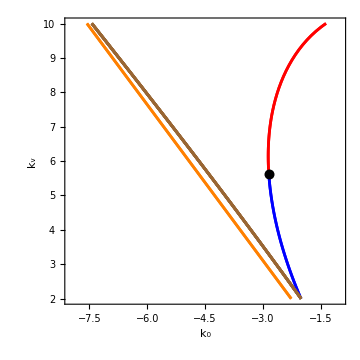
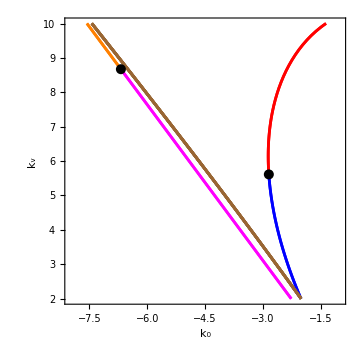

```mathematica
If[Length[critchange130]>=1,
critpoints130=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange130[[critnum]]]}],{critnum,Length[critchange130]}];
]
If[Length[critchange112]>=1,
critpoints112=Table[Graphics[{PointSize[0.02],Point[{par[[1]],par[[2]]}/.critchange112[[critnum]]]}],{critnum,Length[critchange112]}];
]
bifcurveplot130={};
bifcurveplot112={};
GlobalHopfplot={};
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
If[outersolnum==1 || outersolnum==2,
Continue[]
];
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot[Unevaluated @ {
If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]<0 && Chop[omegaNF[time],Choptol]!=0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[omegaNF[time],Choptol]==0 && Chop[muNF[time],Choptol]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[muNF[time]==0 && omegaNF[time]==0 /.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Orange,Magenta,{Black,Dotted},Red,Blue,{Green,Dotted},Brown,Purple,Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
AppendTo[bifcurveplot130,tempplot];
]
]
For[outersolnum=1,outersolnum<=Length[solutioncurves],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurves[[outersolnum]]],innersolnum++,
If[outersolnum==1 || outersolnum==2,
Continue[]
];
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130+C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot[Unevaluated @ {
If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]<0 && Chop[omegaNF[time],Choptol]!=0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[omegaNF[time],Choptol]==0 && Chop[muNF[time],Choptol]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[muNF[time]==0 && omegaNF[time]==0 /.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Orange,Magenta,{Black,Dotted},Red,Blue,{Green,Dotted},Brown,Purple,Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
AppendTo[bifcurveplot112,tempplot];
]
]
For[outersolnum=1,outersolnum<=Length[solutioncurvesGlobalHopf],outersolnum++,
For[innersolnum=1,innersolnum<=Length[solutioncurvesGlobalHopf[[outersolnum]]],innersolnum++,
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->0/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot[Unevaluated @ {If[Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]],If[Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]], If[Chop[omegaNF[time],Choptol]==0/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]]},{time,solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Brown,Purple,Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
AppendTo[GlobalHopfplot,tempplot];
]
]
CreateDocument[Dynamic[plot3],WindowSize->{500,500}];
If[ValueQ[critpoints130] && ValueQ[critpoints112],
plot3=Row[(Show[#1,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[{{bifcurveplot130,GlobalHopfplot,critpoints130},{bifcurveplot112,GlobalHopfplot,critpoints112}},0]]]
If[ValueQ[critpoints130] && ¬ValueQ[critpoints112],
plot3=Row[(Show[#1,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[{{bifcurveplot130,GlobalHopfplot,critpoints130},{bifcurveplot112,GlobalHopfplot}},0]]]
If[¬ValueQ[critpoints130] && ValueQ[critpoints112],
plot3=Row[(Show[#1,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[{{bifcurveplot130,GlobalHopfplot},{bifcurveplot112,GlobalHopfplot,critpoints112}},0]]]
If[¬ValueQ[critpoints130] && ¬ValueQ[critpoints112],
plot3=Row[(Show[#1,ImageSize->Medium,Frame->True,FrameLabel->{ToString[newparam1,StandardForm],ToString[newparam2,StandardForm]},RotateLabel->False,FrameStyle->Directive[FontSize->15],AspectRatio->1]&)/@Flatten[{{bifcurveplot130,GlobalHopfplot},{bifcurveplot112,GlobalHopfplot}},0]]]
```

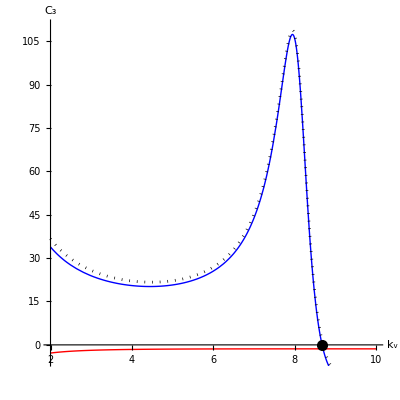

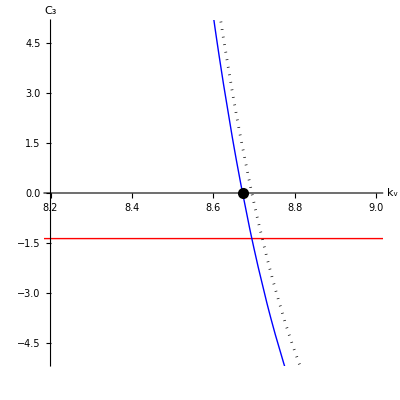

```mathematica
outersolnum=5;
innersolnum=1;
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC112=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130+C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC112alone=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
curves=ParametricPlot[{{par[[2]][time],Re[auxC3[time]]}/.solutioncurves[[outersolnum]][[innersolnum]],{par[[2]][time],Re[auxC112[time]]}/.solutioncurves[[outersolnum]][[innersolnum]],{par[[2]][time],Re[auxC112alone[time]]}/.solutioncurves[[outersolnum]][[innersolnum]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Dotted}},PlotRange->{{lowerbound[[2]],upperbound[[2]]},{-10,10}},AspectRatio->1];
point=Graphics[{PointSize[0.02],Point[{8.671739568778762,0}]}];
Show[curves,point,PlotRange->{{lowerbound[[2]],upperbound[[2]]},{-5,110}},AxesLabel->{ToString[newparam2,StandardForm],"C_3"},BaseStyle->Directive[FontSize->15]]
curves=ParametricPlot[{{par[[2]][time],Re[auxC3[time]]}/.solutioncurves[[outersolnum]][[innersolnum]],{par[[2]][time],Re[auxC112[time]]}/.solutioncurves[[outersolnum]][[innersolnum]],{par[[2]][time],Re[auxC112alone[time]]}/.solutioncurves[[outersolnum]][[innersolnum]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{{Red,Thick},{Blue,Thick},{Black,Dotted}},PlotRange->{{8.2,9},{-5,5}},AspectRatio->1];
Show[curves,point,PlotRange->{{8.2,9},{-5,5}},AxesLabel->{ToString[newparam2,StandardForm],"C_3"},BaseStyle->Directive[FontSize->15]]
```

```mathematica
timesol=NSolve[par[[1]][time]==fifthcoeff132[[2]][[1]][[1]]/.solutioncurves[[5]][[1]],time][[1]];
pval=par[[1]][time]/.solutioncurves[[5]][[1]]/.timesol;
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

```mathematica
C11eval=C11/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.i->ⅈ/.timesol
C112eval=C130+C112/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.timesol
C132eval=C150+C114+C132/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.timesol
```

0.186825-0.0487651 ⅈ

1.00669×10^-6-81.4241 ⅈ

104000.-162532. ⅈ

```mathematica
{Subscript[k, 1][time],Subscript[k, 3][time]}/.solutioncurves[[5]][[1]]/.timesol
```

{-6.68553,8.67174}

```mathematica
timesol
```

{time→77.8273}

```mathematica
{Subscript[k, 1][time],Subscript[k, 3][time],√muNF[time]}/.solutioncurves[[5]][[1]]/.time->77.85
```

{-6.68678,8.67363,0.36907}

```mathematica
(2π)/(√muNF[time])/.solutioncurves[[5]][[1]]/.time->77.85
```

17.0244

```mathematica
timesol2=NSolve[par[[2]][time]==8.7/.solutioncurves[[5]][[1]],time][[1]];
C11eval2=C11/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.i->ⅈ/.timesol2
C112eval2=C130+C112/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.timesol2
C132eval2=C150+C114+C132/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.timesol2
{Subscript[k, 1][time],Subscript[k, 3][time],√muNF[time]}/.solutioncurves[[5]][[1]]/.timesol2
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.186347-0.0485564 ⅈ

-1.67308-79.0955 ⅈ

84846.8-154892. ⅈ

{-6.70425,8.7,0.369059}

```mathematica
timesol2=NSolve[par[[2]][time]==8.68/.solutioncurves[[5]][[1]],time][[1]];
C11eval2=C11/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.i->ⅈ/.timesol2
C112eval2=C130+C112/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.timesol2
C132eval2=C150+C114+C132/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.solutioncurves[[5]][[1]]/.timesol2
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

0.186685-0.048704 ⅈ

-0.511085-80.7371 ⅈ

98087.2-160395. ⅈ

```mathematica
{par[[1]][time],par[[2]][time]}/.solutioncurves[[5]][[1]]/.timesol2
```

{-6.69101,8.68}

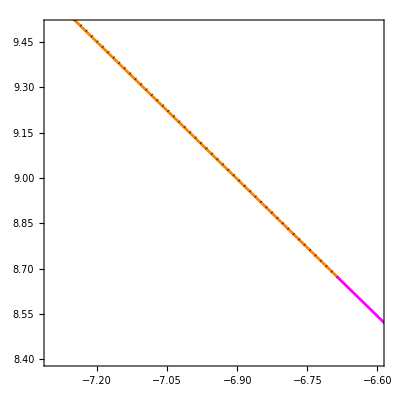

```mathematica
outersolnum=5;
innersolnum=1;
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC11=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C11/.i->ⅈ/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130+C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC5=C150+C114+C132/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]/.timesol;
tempplot1=Quiet@ParametricPlot[Unevaluated @ {
If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]<0 && Chop[omegaNF[time],Choptol]!=0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[omegaNF[time],Choptol]==0 && Chop[muNF[time],Choptol]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[muNF[time]==0 && omegaNF[time]==0 /.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Orange,Magenta,{Black,Dotted},Red,Blue,{Green,Dotted},Brown,Purple,Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
tempplot2=Quiet@ParametricPlot[If[Re[auxC3[time]]*Re[auxC5]<0,{par[[1]][time]+Re[auxC3[time]]^2/(4*Re[auxC11[time]]*Re[auxC5]),par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Dotted,Black},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
(*outersolnum=1;
innersolnum=1;
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->0/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]);
tempplot3=Quiet@ParametricPlot[Unevaluated @ {If[Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]],If[Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]], If[Chop[omegaNF[time],Choptol]==0/.solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]]]},{time,solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurvesGlobalHopf[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Brown,Purple,Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];*)
Show[tempplot1,tempplot2,PlotRange->{{-7.3,-6.6},{8.4,9.5}},AspectRatio->1,Frame->True]
```

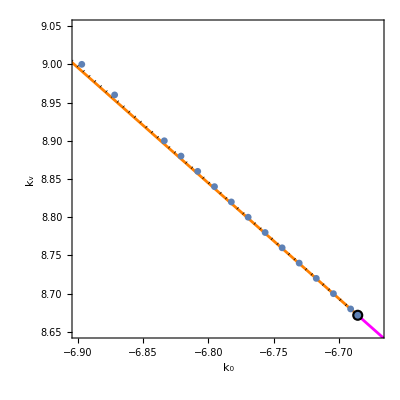

```mathematica
Needs["Splines`"]
table={{-6.68552,8.671739568778754},{-6.69098,8.68},{-6.70417,8.7},{-6.71732,8.72},{-6.73042,8.74},{-6.74349,8.76},{-6.75651,8.78},{-6.76954,8.8},{-6.78244,8.82},{-6.79534,8.84},{-6.80822, 8.86},{-6.82103, 8.88},{-6.83382,8.9},{-6.87192,8.96},{-6.89711,9.0}};
(*tablespline=SplineFit[table,Cubic];
tableplot=ParametricPlot[tablespline[time],{time,0,Length[table]}];*)
(*tableplot=Plot[Interpolation[table,Method->"Spline"][x],{x,-6.78173,-6.66837}];*)
tableplot=ListPlot[table,PlotMarkers->{Automatic,7}];
Show[{tempplot1,tempplot2,critpoints112,tableplot}//Flatten,PlotRange->{{-6.9,-6.67},{8.65,9.05}},Frame->True,FrameLabel->{"k_0","k_v"},RotateLabel->False,FrameStyle->Directive[FontSize->20],AspectRatio->1]
```

```mathematica
outersolnum=5;
innersolnum=1;
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC11=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C11/.i->ⅈ/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130+C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC5=C150+C114+C132/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]/.timesol;
tempplot2=Quiet@ParametricPlot[If[Re[auxC3[time]]*Re[auxC5]<0,{par[[1]][time]+Re[auxC3[time]]^2/(4*Re[auxC11[time]]*Re[auxC5]),par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Dotted,Black},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}];
```

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

General::stop: Further output of NSolve::ifun will be suppressed during this calculation.

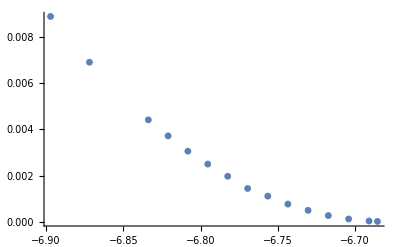

-Graphics-

```mathematica
Needs["Splines`"]
table={{-6.68552,8.671739568778754},{-6.69098,8.68},{-6.70417,8.7},{-6.71732,8.72},{-6.73042,8.74},{-6.74349,8.76},{-6.75651,8.78},{-6.76954,8.8},{-6.78244,8.82},{-6.79534,8.84},{-6.80822, 8.86},{-6.82103, 8.88},{-6.83382,8.9},{-6.87192,8.96},{-6.89711,9.0}};
newtable={};
For[solnum=1,solnum<=Length[table],solnum++,
auxtime=NSolve[par[[1]][time]==table[[solnum]][[1]]/.solutioncurves[[5]][[1]],time][[1]];
par2val=par[[2]][time]/.solutioncurves[[5]][[1]]/.auxtime;
AppendTo[newtable,{table[[solnum]][[1]],table[[solnum]][[2]]-par2val}];
]
(*tablespline=SplineFit[table,Cubic];
tableplot=ParametricPlot[tablespline[time],{time,0,Length[table]}];*)
(*tableplot=Plot[Interpolation[table,Method->"Spline"][x],{x,-6.78173,-6.66837}];*)
tableplot=ListPlot[table,PlotMarkers->{Automatic,7}];
tableplot2=ListPlot[newtable,PlotMarkers->{Automatic,7}]
Show[{tempplot1,tempplot2,critpoints112,tableplot}//Flatten,PlotRange->{{-6.9,-6.67},{8.65,9.05}},Frame->True,FrameLabel->{"k_0","k_v"},RotateLabel->False,FrameStyle->Directive[FontSize->20],AspectRatio->1]
```

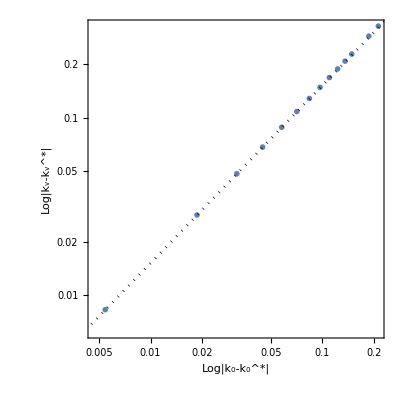

```mathematica
outersolnum=5;
innersolnum=1;
auxC11=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C11/.i->ⅈ/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130+C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC5=C150+C114+C132/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]/.timesol;
logtable=ListLogLogPlot[Table[{Abs[table[[pnum]][[1]]-fifthcoeff132[[2]][[1]][[1]]],Abs[table[[pnum]][[2]]-fifthcoeff132[[2]][[1]][[2]]]},{pnum,Length[table]}],PlotMarkers->{●,4}];
logtempplot2=Quiet@ParametricPlot[If[Re[auxC3[time]]*Re[auxC5]<0,{Log[Abs[par[[1]][time]+Re[auxC3[time]]^2/(4*Re[auxC11[time]]*Re[auxC5])-fifthcoeff132[[2]][[1]][[1]]]],Log[Abs[par[[2]][time]-fifthcoeff132[[2]][[1]][[2]]]]}/. solutioncurves[[outersolnum]][[innersolnum]]],{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Dotted,Black}];
Show[logtable,logtempplot2,Frame->True,AspectRatio->1,BaseStyle->Directive[FontSize->20],FrameLabel->{"Log|k_0-k_0^*|","Log|k_v-k_v^*|"},FrameTicks->{{Automatic,None}, {{-5,-4,-3,-2},None}}]
```

```mathematica
auxC3[time]/.time->77.82733799316668
{par[[1]][time],par[[2]][time]}/.solutioncurves[[5]][[1]]/.time->77.82733799316668
NSolve[par[[1]][time]==-6.58/.solutioncurves[[5]][[1]],time]
```

6.43929×10^-15-81.4241 ⅈ

{-6.68553,8.67174}

NSolve::ifun: Inverse functions are being used by NSolve, so some solutions may not be found; use Reduce for complete solution information.

{{time→75.9141}}

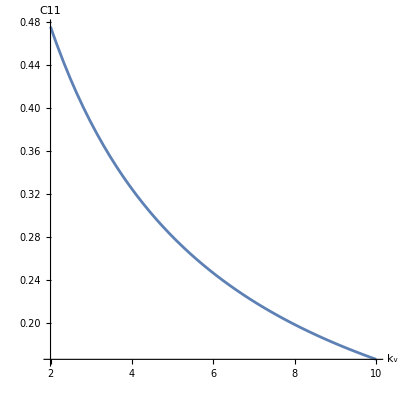

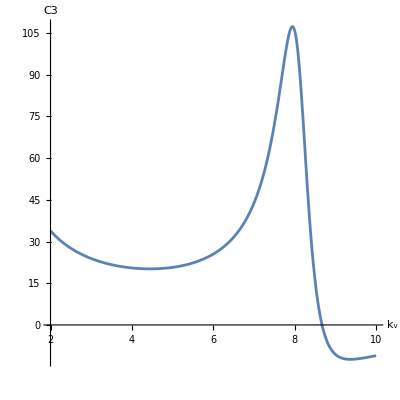

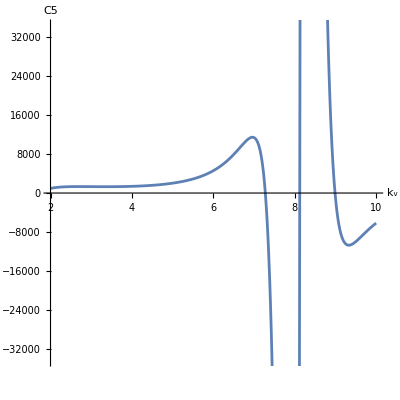

```mathematica
outersolnum=5;
innersolnum=1;
auxC11=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C11/.i->ⅈ/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130+C112/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC5=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C150+C114+C132/.eq/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
ParametricPlot[{par[[2]][time],Re[auxC11[time]]}/.solutioncurves[[outersolnum]][[innersolnum]],{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,AxesLabel->{"k_v","C11"}]
ParametricPlot[{par[[2]][time],Re[auxC3[time]]}/.solutioncurves[[outersolnum]][[innersolnum]],{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,AxesLabel->{"k_v","C3"}]
ParametricPlot[{par[[2]][time],Re[auxC5[time]]}/.solutioncurves[[outersolnum]][[innersolnum]],{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},AspectRatio->1,AxesLabel->{"k_v","C5"}]
```

```mathematica
fixedpar
auxvar={par[[1]],par[[2]],muNF,omegaNF,u};
auxvar=Table[{auxvar[[vnum]]->(auxvar[[vnum]][time]/.solutioncurves[[outersolnum]][[innersolnum]]/.time->68)},{vnum,Length[auxvar]}]//Flatten
```

{k_4→3,τ→10,D_1→1,D_2→1,D_3→60}

{k_1→-6.14351,k_3→7.85338,muNF→0.136461,omegaNF→0.870687,u→-0.661258}

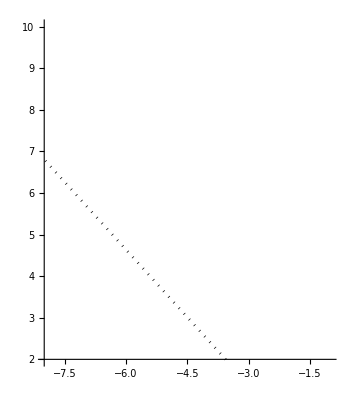

```mathematica
outersolnum=2;
innersolnum=1;
auxnonzero=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (nonzero/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
auxC3=Compile[{time},#,RuntimeOptions->"EvaluateSymbolically"->False]&@ (C130/.fixedpar/.par[[1]]->par[[1]][time]/.par[[2]]->par[[2]][time]/.muNF->muNF[time]/.omegaNF->omegaNF[time]/.variabledependence/.solutioncurves[[outersolnum]][[innersolnum]]);
tempplot=Quiet@ParametricPlot[Unevaluated @ {
If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]],If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]<0 && Chop[omegaNF[time],Choptol]!=0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[muNF[time],Choptol]>0 && Chop[omegaNF[time],Choptol]==0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[auxnonzero[time],Choptol]!=0 && Chop[omegaNF[time],Choptol]==0 && Chop[muNF[time],Choptol]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]<0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[Chop[muNF[time],Choptol]==0 && Chop[omegaNF[time],Choptol]!=0 && Re[auxC3[time]]>0/.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]], If[muNF[time]==0 && omegaNF[time]==0 /.solutioncurves[[outersolnum]][[innersolnum]],{par[[1]][time],par[[2]][time]}/. solutioncurves[[outersolnum]][[innersolnum]]]},{time,solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[1]],solutioncurves[[outersolnum]][[innersolnum]][[1]][[2]]["Domain"][[1]][[2]]},PlotStyle->{Orange,Magenta,{Black,Dotted},Red,Blue,{Green,Dotted},Brown,Purple,Gray},PlotRange->{{lowerbound[[1]],upperbound[[1]]},{lowerbound[[2]],upperbound[[2]]}}]
```